```mathematica
pu = (1+m)/2;
pd = (1-m)/2;
FullSimplify[pu+pd]
puu = ((1+m)^2+c)/4;
pdd = ((1-m)^2+c)/4;
pud = pdu =(1-m^2-c)/4;
FullSimplify[puu + pdd+ pud + pdu]
pugu = puu/pu
pugd = pdu/pd;
pdgu = pud/pu;
pdgd = pdd/pd;
c=0;
FullSimplify[pugu]
FullSimplify[pugd]
FullSimplify[pdgu]
FullSimplify[pdgd ]
Clear[c]
FullSimplify[pugu+pdgu]
```

1

1

(c+(1+m)^2)/(2 (1+m))

(1+m)/2

(1+m)/2

(1-m)/2

(1-m)/2

1

```mathematica
m = 0;
c = -1;
pugu
pdgu
Clear[m,c]
```

0

1

```mathematica
pdud=pd*pugd*pdgu
pduu=pd*pugd*pugu;
pddu=pd*pdgd*pugd;
pudu=pu*pdgu*pugd;
c=0;
FullSimplify[pdud]
FullSimplify[pduu]
FullSimplify[pddu]
FullSimplify[pudu]
Clear[c]
```

((1-c-m^2)^2)/(8 (1+m))

1/8 (-1+m)^2 (1+m)

-1/8 (1+m) (-1+m^2)

1/8 (-1+m)^2 (1+m)

-1/8 (-1+m) (1+m)^2

```mathematica
G=2*(pdud+pddu+pudu) + 4*(pduu);
FullSimplify[G]
c = 0;
FullSimplify[G]
Clear[c]
```

-((-1+c+m^2) (c+(1+m) (5+m)))/(4 (1+m))

-1/4 (-1+m) (1+m) (5+m)

0.1

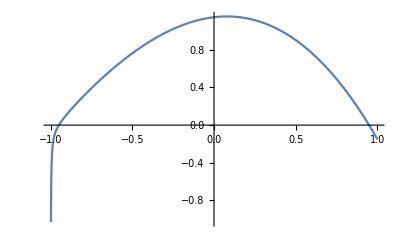

```mathematica
c =.1
Plot[G,{m,-1,1}]
Clear[c]
```

```mathematica
m = 1;
G
Clear[m]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression c^2/16+ComplexInfinity+ComplexInfinity encountered.

Indeterminate

```mathematica
a = {{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
FullSimplify[pdd*pdu/pd]
```

((c+(-1+m)^2) (-1+c+m^2))/(8 (-1+m))

```mathematica
pddu
```

((c+(1-m)^2) (1-c-m^2))/(8 (1-m))

```mathematica
pdd
pdu
pd
```

1/4 (c+(1-m)^2)

1/4 (1-c-m^2)

(1-m)/2